```mathematica
$Version
Clear["Global`*"]
```

14.0.0 for Microsoft Windows (64-bit) (December 13, 2023)

```mathematica
LatticeEndIndex = 100;
```

```mathematica
J[n_,α_]:=J[n,α]=1/Abs[n]^(1+α);
K[α_]:=Sum[J[n,α],{n,1,LatticeEndIndex}];
```

```mathematica
wB = 1/2;
wA = 2 wB;
```

```mathematica
q[0,ϵ_,α_,wA_]:=Sqrt[wA+2 ϵ  K[α]];
q[n_Integer?Positive,ϵ_,α_,wA_]:=q[n,ϵ,α,wA]=ϵ  (J[n,α]*q[0,ϵ,α,wA]+Sum[(J[n-m,α]+J[n+m,α])*q[m,ϵ,α,wA],{m,1,n-1}])/(ϵ  (2K[α]-J[2n,α])+wA)//Simplify
```

```mathematica
g[0,ϵ_,α_,wB_]:=Sqrt[wB+ϵ(2K[α]-J[1,α])]
g[1,ϵ_,α_,wB_]:=Sqrt[wB+ϵ(2K[α]-J[1,α])]
g[n_Integer?Positive,ϵ_,α_,wB_]:=g[n,ϵ,α,wB]= ϵ Sum[(J[n-m,α]+J[n+m-1,α])*g[m,ϵ,α,wB],{m,1,n-1}]/(ϵ  (2K[α]-J[2n-1,α])+wB)//Simplify
```

```mathematica
EA[ϵ_,α_,wA_]:=ϵ Sum[1/n^(1+α)Abs[ q[n,ϵ,α,wA] - q[0,ϵ,α,wA] ]^2 + 1/2 Sum[If[m!=n,(1/Abs[n-m]^(1+α)+1/Abs[n+m]^(1+α))*Abs[ q[n,ϵ,α,wA]- q[m,ϵ,α,wA]]^2,0],{m,1,LatticeEndIndex}],{n,1,LatticeEndIndex }]-(1/4 q[0,ϵ,α,wA]^4+1/2 Sum[q[n,ϵ,α,wA]^4,{n,1,LatticeEndIndex }])
```

```mathematica
EB[ϵ_,α_,wB_]:= ϵ Sum[(1/n^(1+α)+1/(n-1)^(1+α))Abs[g[n,ϵ,α,wB] - g[0,ϵ,α,wB]]^2+1/2 Sum[If[m!=n,(1/Abs[n-m]^(1+α)+1/Abs[n+m-1]^(1+α))*Abs[g[n,ϵ,α,wB]-g[m,ϵ,α,wB]]^2,0],{m,2,LatticeEndIndex}],{n,2,LatticeEndIndex}]-1/2 Sum[g[n,ϵ,α,wB]^4,{n,1,LatticeEndIndex}]
```

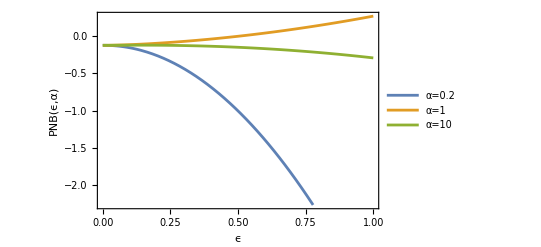

```mathematica
Plot[{EA[ϵ,0.2,wA]-EB[ϵ,0.2,wB],EA[ϵ,1,wA]-EB[ϵ,1,wB],EA[ϵ,10,wA]-EB[ϵ,10,wB]},{ϵ,0,1},PlotLegends->{"α=0.2","α=1","α=10"},Frame->True,FrameStyle->Thick,FrameLabel->{Style["ϵ",16,Bold],
Rotate[Style["PNB(ϵ,α)",16,Bold], -90 Degree]}]
```

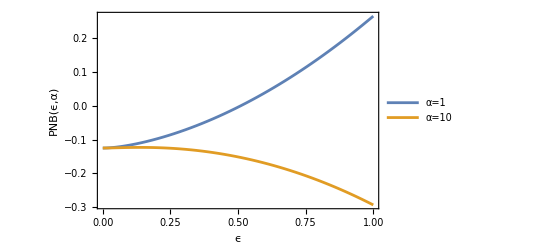

```mathematica
Plot[{EA[ϵ,1,wA]-EB[ϵ,1,wB],EA[ϵ,10,wA]-EB[ϵ,10,wB]},{ϵ,0,1},PlotLegends->{"α=1","α=10"},Frame->True,FrameStyle->Thick,FrameLabel->{Style["ϵ",16,Bold],
Rotate[Style["PNB(ϵ,α)",16,Bold], -90 Degree]}]
```